```mathematica
<<NumericalCalculus`
```

```mathematica
(*polynomial determination*)
```

```mathematica
c=theC;
phiSol=First[NDSolve[{(1-η^2)D[f[η],{η,2}]-2η D[f[η],η]-(-Λ[c]+c η^2)f[η]==0,f[0.999999999]==1,f[-0.999999999]==1},f,{η,-0.999999999,0.999999999}]]
```

```mathematica
list={};
list2={};
minC=-35;
maxC=-1;
list={};
list2={};
step=1;
For[c=minC,c≤maxC,c+=step,
phiSol=First[NDSolve[{(1-η^2)D[f[η],{η,2}]-2η D[f[η],η]-(-Λ+c η^2)f[η]==0,f[0.999999999]==1,f[-0.999999999]==1},f,{η,-0.999999999,0.999999999}]];
temp[ξ_]=g[ξ]/.sol;
AppendTo[list, ND[temp[ξ],ξ,1.000001]-(c-Λ[c])/2];
AppendTo[list2, c];
];
```

```mathematica
xy=Thread @ {list2,Flatten[list]};
int=Interpolation[xy];
theC=x/.FindRoot[D[int[x]]==0,{x,minC}];
ListPlot[xy]
```

InterpolatingFunction::dmval: Input value {0.34} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.278223} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.536753} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

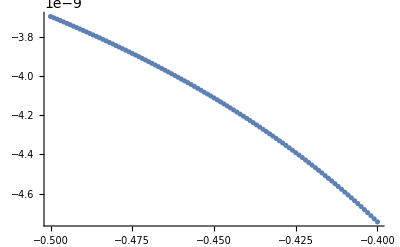

```mathematica
minΛ=-0.5;
maxΛ=-0.4;
c=-1;
list={};
list2={};
step=0.001;
For[Λ=minΛ,Λ≤maxΛ,Λ+=step,
phiSol=First[NDSolve[{(1-η^2)D[f[η],{η,2}]-2η D[f[η],η]-(-Λ+c η^2)f[η]==0,f[0.999999999]==1,f[-0.999999999]==1},f,{η,-0.999999999,0.999999999}]];
temp[η_]=f[η]/.phiSol;
the[η_]=D[temp[η],η];
AppendTo[list, the[-0.00000001]-the[0.00000001]];
AppendTo[list2, Λ];
];
xy=Thread @ {list2,Flatten[list]};
int=Interpolation[xy];
theC=x/.FindRoot[D[int[x]]==0,{x,0.34}];
ListPlot[xy]
```

```mathematica
theC
```

-0.300565

```mathematica
list
```

{-1.25401×10^7,4.40351×10^7,-1.19842×10^7,-2.81223×10^7,-1.39863×10^7,-1.11516×10^7,-1.45326×10^7,-1.62029×10^7,-1.32232×10^7,-1.21852×10^7,-4.30223×10^6,-1.37315×10^7,-2.05523×10^7,-1.15636×10^7,7.78345×10^7,-2.13712×10^7,-1.89462×10^7,-3.56029×10^6,-1.22876×10^7,-3.23271×10^6,-8.40028×10^6,-4.15414×10^6,-3.16843×10^6,-7.32266×10^6,-7.53606×10^6,1.18234×10^6,-5.33308×10^6,-3.78555×10^6,-2.43488×10^6,-6.46581×10^6,-6.02529×10^6,-2.16532×10^6,-5.55012×10^6,-4.79234×10^6,4.61948×10^6,-4.94698×10^6,-5.01158×10^6,-1.24036×10^6,6.65693×10^6,-3.79269×10^6,-1.33518×10^6,-3.03687×10^6,-2.90653×10^6,1.60349×10^6,-2.83251×10^6,1.12457×10^8,744487.,-2.42527×10^6,-1.10572×10^6,-1.11224×10^6,150635.,-156412.,110940.,9639.52,1.14513×10^6,1.23137×10^6,1.50463×10^6,3.74161×10^6,2.31668×10^6,2.62392×10^6,3.10104×10^6,3.40961×10^6,4.40949×10^6,8.76279×10^6,4.66491×10^6,1.10408×10^7,2.12772×10^6,5.5879×10^6,7.62571×10^6,7.15347×10^6,6.91499×10^6,-5.10171×10^7,1.52115×10^7,-4.02594×10^6,-8.53851×10^6,-4.52726×10^7,9.5165×10^6,1.02835×10^7,1.1154×10^7,1.16722×10^7,4.57193×10^6,1.94634×10^7,2.52908×10^7,1.75782×10^7,1.5017×10^7,-4.77647×10^7,1.88039×10^7,6.82266×10^6,1.65716×10^7,1.72799×10^7,1.84801×10^7,1.93088×10^7,8.33522×10^6,8.04282×10^6,2.69115×10^7,1.5871×10^7,2.27355×10^7,2.35007×10^7,2.21237×10^7,-9.32712×10^6,5.71339×10^7}

```mathematica
FindFit[xy,a*(x+b)^2+d, {a, b, d},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→1.36617×10^6,b→82.2033,d→-9.15092×10^9}

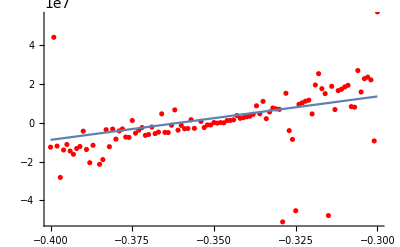

```mathematica
Show[ListPlot[xy,PlotStyle->Red],Plot[a (x+b)^2+d/.{a->1.3661738137056343*^6,b->82.2033068223354,d->-9.150921264385427*^9},{x,-0.4,-0.29999999999999993}]]
```

-0.33

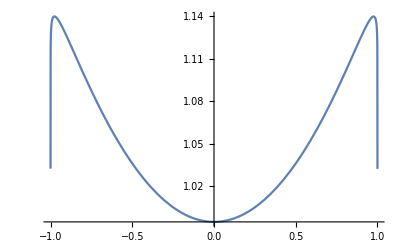

```mathematica
c=-1;
Λ=-0.33
phiSol=First[NDSolve[{(1-η^2)D[f[η],{η,2}]-2η D[f[η],η]-(-Λ+c η^2)f[η]==0,f[0.999999999]==1,f[-0.999999999]==1},f,{η,-0.999999999,0.999999999}]];
temp[η_]=f[η]/.phiSol;
Plot[temp[η],{η,-1,1}]
```

```mathematica
ND[temp[η],η,-0.0001]
```

-0.0000408457

```mathematica
the[η_]=D[temp[η],{η}]
```

InterpolatingFunction[…][η]

```mathematica
temp[-0.0001]
```

0.994897

```mathematica
the[-0.0001]
```

-0.000040753

```mathematica
the[0.0001]
```

0.0000249102